```mathematica
<< MASStoolbox`Style`
<< MASStoolbox`
SetDirectory[NotebookDirectory[]];
SetDirectory[".."];
<< util`
```

# SB2 Systems Biology : Simulation of Dynamic Network States

## Hemoglobin

### Construct model

```mathematica
chemicalFormulas={m["dhb", "c"] -> "&Hb&C3H3O10P2", m["dpg23", "c"] -> "C3H3O10P2", m["h", "c"] -> "H", m["hbo24", "c"] -> "&Hb&O8", 
 m["o2", "c"] -> "O2", m["pg13", "c"] -> "C3H4O10P2", m["pg3", "c"] -> "C3H4O7P", m["phos", "c"] -> "HO4P", 
 m["h2o", "c"] -> "H2O", m["hb", "c"] -> "&Hb&", m["hbo2", "c"] -> "&Hb&O2", m["hbo22", "c"] -> "&Hb&O4", 
 m["hbo23", "c"] -> "&Hb&O6"};
```

```mathematica
rxns=str2mass/@{"vdpgase: dpg23_c + h2o_c <=> pg3_c + phos_c","vdpgm: pg13_c <=> dpg23_c + h_c","vhbdpg: dpg23_c + hb_c <=> dhb_c","vhbo1: hb_c + o2_c <=> hbo2_c","vhbo2: hbo2_c + o2_c <=> hbo22_c","vhbo3: hbo22_c + o2_c <=> hbo23_c","vhbo4: hbo23_c + o2_c <=> hbo24_c","vo2: o2_c <=> 0"};
```

```mathematica
conc={dhb^c->0.04620957029335471Millimole Liter^-1,hb^c->0.059625251991425425Millimole Liter^-1,hbo2^c->0.05008521167279736Millimole Liter^-1,hbo22^c->0.07362526115901212Millimole Liter^-1,hbo23^c->0.26284218233767326Millimole Liter^-1,hbo24^c->6.807612522545737Millimole Liter^-1,o2^c->0.0200788Millimole Liter^-1,dpg23^c->3.1Millimole Liter^-1,pg13^c->0.000243 Millimole Liter^-1,pg3^c->0.0773 Millimole Liter^-1,phos^c->2.5 Millimole Liter^-1,h^c->0.00008997573444801929 Millimole Liter^-1,h2o^c->1. Millimole Liter^-1};
```

```mathematica
param={Underscript[Volume, c]->Liter,Underscript[K, vdpgase]->∞ Millimole Liter^-1,Underscript[K, vdpgm]->∞,Underscript[K, vhbdpg]->1/4 Liter Millimole^-1,Underscript[K, vhbo1]->41.835169432436196 Liter Millimole^-1,Underscript[K, vhbo2]->73.21154650676336 Liter Millimole^-1,Underscript[K, vhbo3]->177.79947008785382 Liter Millimole^-1,Underscript[K, vhbo4]->1289.9177241667828 Liter Millimole^-1,Underscript[K, vo2]->1,Subscript[k, vdpgase]^⟶->0.14225806451612902 Hour^-1,Subscript[k, vdpgm]^⟶->1814.8148148148148 Hour^-1,Subscript[k, vhbo1]^⟶->506935.270702259 Liter Hour^-1 Millimole^-1,Subscript[k, vhbo2]^⟶->511077.050923776 Liter Hour^-1 Millimole^-1,Subscript[k, vhbo3]^⟶->509243.459567699 Liter Hour^-1 Millimole^-1,Subscript[k, vhbo4]^⟶->501595.340624411 Liter Hour^-1 Millimole^-1,Subscript[k, vhbdpg]^⟶->519612.560391792 Liter Hour^-1 Millimole^-1,Subscript[k, vo2]^⟶->509725.707725914 Hour^-1,m["o2","Xt"]->0.0200788Millimole Liter^-1};
```

```mathematica
hemoglobin=constructModel[rxns,InitialConditions->conc,Parameters->param,ElementalComposition->chemicalFormulas,Ignore->{m["h2o","c"],m["h","c"]},UnitChecking->True];
```

### Key ratios

```mathematica
keyRatios={"r_OHb"->(hbo2^c+2 hbo22^c+3 hbo23^c+4 hbo24^c)/(4*7.3)};
```

### Analyze model

```mathematica
hemoglobinStandalone=hemoglobin;
updateBoundaryConditions[hemoglobinStandalone,{dpg23^c,pg13^c,pg3^c,phos^c,h2o^c,h^c}]
```

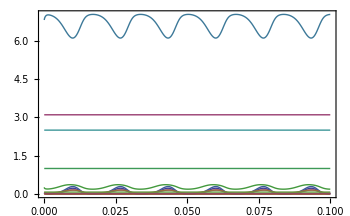

```mathematica
{concSol,fluxSol}=simulate[stripUnits@hemoglobinStandalone,{t,0,.1},Parameters->{m["o2","Xt"]->(30*Cos[120*Pi*t]+70)*0.00028684},MaxSteps->100000];
plotSimulation[concSol,PlotFunction->Plot,Tooltipped->False]
```

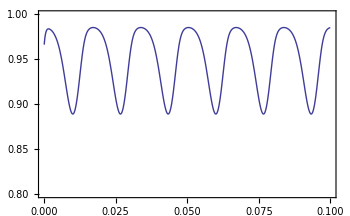

```mathematica
plotSimulation[keyRatios/.concSol,PlotFunction->Plot,PlotRange->{All,{0.8,1}}]
```

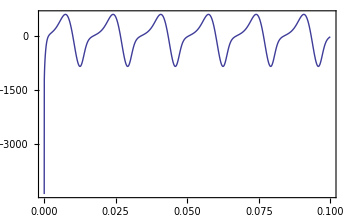

```mathematica
plotSimulation[filter[fluxSol,{v["vo2"]}],PlotFunction->Plot]
```

### Conversion factor

```mathematica
0.0031*40 *10*0.0554
0.0031*40 *100*0.0554
```

0.068696

0.68696

```mathematica
0.0031*40
```

0.124

```mathematica
0.0031*40(*mmHg*)*10(*to get liter*)
0.0031*100(*mmHg*)*10(*to get liter*)
```

1.24

3.1

```mathematica
N@ConvertTemperature[37 Celsius,Kelvin]
```

310.15 Kelvin

```mathematica
Convert[Mean[{0.04,0.12}]Millimole Liter^-1,Mole Liter^-1]
```

0.00008 Mole Liter^-1

```mathematica
SI[(1Atmosphere*1.24Milli Liter)/(MolarGasConstant*310.15 Kelvin)]
```

0.0487228 Millimole

```mathematica
SI[(1Atmosphere*3.1Milli Liter)/(MolarGasConstant*310.15 Kelvin)]
```

0.121807 Millimole

```mathematica
Convert[1.3*^-3Mole Liter^-1 Atmosphere^-1*Convert[40MillimeterMercury,Atmosphere],Millimole Liter^-1]
Convert[1.3*^-3Mole Liter^-1 Atmosphere^-1*Convert[100MillimeterMercury,Atmosphere],Millimole Liter^-1]
```

0.0684211 Millimole Liter^-1

0.171053 Millimole Liter^-1

```mathematica
Convert[0.136Mole Liter^-1,Millimole Liter^-1]
```

0.1768 Millimole Liter^-1

### Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../../models/SB2/Hemoglobin.m.gz",hemoglobin]
```

../../models/SB2/Hemoglobin.m.gz